## 1. 解析棋谱 - 并导出JSON

## 1.1 读取数据

### 1.1.1 读取数据

```mathematica
Quiet[Remove["Global`*"]];
SetDirectory[NotebookDirectory[]];
Needs["DatabaseLink`"]
conn=OpenSQLConnection["data_from_sina_go_chess"];

(*
输出：
{
{id,chess_manual},
...
}
*)
strDatas=SQLExecute[conn,"select id, chess_manual from go_chess_manual where match_name like '%世界AlphaGo0历程40模块40天%' order by match_date,match_name","GetAsStrings"->True];
```

### 1.1.2 导出JSON

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"package","go-chess.wl"}]];


goChess`SGFExportJSON[FileNameJoin[{NotebookDirectory[],"export-data",StringTemplate["go-chess-manual-``.json"][#[[1]]]}],#[[1]],#[[2]]]&/@strDatas
```

{D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41341.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41340.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41339.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41338.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41337.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41336.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41335.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41334.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41333.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41332.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41331.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41330.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41329.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41328.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41327.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41326.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41325.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41324.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41323.json,D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41322.json}

## 1.2 SGF to JSON

### 1.2.1 f-从SGF中提取信息

```mathematica
(*输入：一盘字符串格式的SGF围棋数据*)
(*输出：比赛信息 info，棋谱信息 data，以及一些常量 db_id, letter_upper_case, letter_lower_case, position_around, position_to_xy, position_to_rc *)
fSGF2Dict[sgf_String]:=Module[{
goInfo=<||>,data,
id=0,

(*位置用到的字母，及相邻字母*)
dicLetter=<|{"A"->{"B"}}~Join~(#2->{#1,#3}&@@@Partition[CharacterRange["A","S"],3,1])~Join~{"S"->{"R"}}|>,

(*位置，及邻位*)
dicPositionAround,

(*位置，对应的数字位置，pd，先列后行，方便Graphics的xy坐标绘图，矩阵绘图需要转换坐标*)
dicPositionToXY,

(*位置，对应的数字位置，pd，先行后列，直接对应矩阵的行列*)
dicPositionToRC

},
dicPositionAround=<|
Flatten@Outer[
#1<>#2->Flatten[{Thread[#1->dicLetter[#2]],Thread[dicLetter[#1]->#2]}/.Rule->StringJoin]&,
Keys[dicLetter],
Keys[dicLetter]
]
|>;

dicPositionToXY=<|#->{0,20}-{-1,1}(ToCharacterCode[#]-64)&/@Keys[dicPositionAround]|>;

dicPositionToRC=<|#->RotateLeft@ToCharacterCode[#]-64&/@Keys[dicPositionAround]|>;

AssociateTo[goInfo,<|"letter_upper_case"->dicLetter|>];
AssociateTo[goInfo,<|"letter_lower_case"->dicLetter|>];
AssociateTo[goInfo,<|"position_around"->dicPositionAround|>];
AssociateTo[goInfo,<|"position_to_xy"->dicPositionToXY|>];
AssociateTo[goInfo,<|"position_to_rc"->dicPositionToXY|>];


AssociateTo[goInfo,<|
"info"-><|
"执黑棋手"->StringCases[sgf,RegularExpression["PB\\[([^]]+)\\]"]:>"$1"][[1]],
"黑棋段位"->If[StringCases[sgf,RegularExpression["BR\\[([^]]+)\\]"]:>"$1"]=={},"无段",StringCases[sgf,RegularExpression["BR\\[([^]]+)\\]"]:>"$1"][[1]]],
"执白棋手"->StringCases[sgf,RegularExpression["PW\\[([^]]+)\\]"]:>"$1"][[1]],
"白棋段位"->If[StringCases[sgf,RegularExpression["WR\\[([^]]+)\\]"]:>"$1"]=={},"无段",StringCases[sgf,RegularExpression["WR\\[([^]]+)\\]"]:>"$1"][[1]]],

"比赛结果"->StringCases[sgf,RegularExpression["RE\\[([^]]+)\\]"]:>"$1"][[1]],
"比赛日期"->StringCases[sgf,RegularExpression["RD\\[([^]]+)\\]"]:>"$1"][[1]],
"比赛名称"->StringCases[sgf,RegularExpression["TE\\[([^]]+)\\]"]:>"$1"][[1]]
|>
|>];

data=<|StringCases[sgf,RegularExpression[";(\\w)\\[(\\w{2})\\]"]:>(++id-><|
"id"->id,(*步数*)
"color"->ToUpperCase["$1"],
"position_letter"->ToUpperCase["$2"],
"position_xy"->Lookup[dicPositionToXY,ToUpperCase["$2"],{0,0}],(*停着，{0,0}*)
"position_matirx"->Lookup[dicPositionToRC,ToUpperCase["$2"],{0,0}],(*停着，{0,0}*)
"group_id"->0,
"breath_left"->Length[Lookup[dicPositionAround,ToUpperCase["$2"],{}]],(*停着，0*)
"around_letter"->Lookup[dicPositionAround,ToUpperCase["$2"],{}](*停着，{}*)
|>)]|>;
data=DeleteCases[data,x_/;x["position_xy"]=={0,0}];
AssociateTo[goInfo,<|"data"->data|>];

goInfo
];
```

{letter_upper_case,letter_lower_case,position_around,position_to_xy,position_to_rc,info,data}

<|执黑棋手→AlphaGo0,黑棋段位→无段,执白棋手→AlphaGo0,白棋段位→无段,比赛结果→黑中盘胜,比赛日期→2017-10-19,比赛名称→世界AlphaGo0历程40模块40天01|>

<|1→<|id→1,color→B,position_letter→KP,position_xy→{11,4},position_matirx→{16,11},group_id→0,breath_left→4,around_letter→{KO,KQ,JP,LP}|>,2→<|id→2,color→W,position_letter→PI,position_xy→{16,11},position_matirx→{9,16},group_id→0,breath_left→4,around_letter→{PH,PJ,OI,QI}|>,532,541→<|id→541,color→B,position_letter→SE,position_xy→{19,15},position_matirx→{5,19},group_id→0,breath_left→3,around_letter→{SD,SF,RE}|>|>
 |  |  |  |

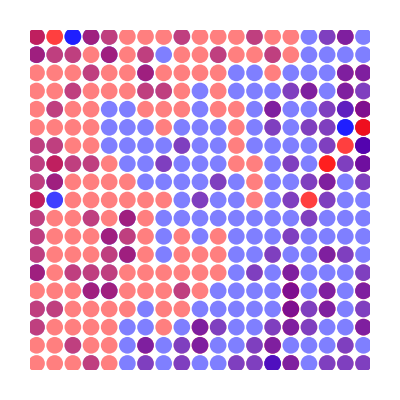

```mathematica
goDict=fSGF2Dict[strDatas[[1,2]]];
Keys[goDict]
goDict["info"]
goDict["data"]
Graphics[{If[#["color"]=="B",Blue,Red],Opacity[0.5],PointSize[0.03],Point[#["position_xy"]]}&/@Values[goDict["data"]]]
```

```mathematica
(*将1份SGF围棋谱转化为后面使用JSON*)
```

### 1.1.2 f-提子

```mathematica
(*输入：棋盘原状态，当前落子。详情参见后面的测试部分*)
(*输出[graph]：每步落子后的棋盘状态*)
fGoGraph[oldData_,piece_]:=Module[{
newData=oldData,
(*棋盘上的棋子，含新子*)
piecesOnCheckerboard=oldData["pieces_on_checkerboard"]~Join~{piece},
piecesOnCheckerboardLetter=#["position_letter"]&/@oldData["pieces_on_checkerboard"]~Join~{piece},
newIDGraph=oldData["id_graph"],

pieceID=piece["id"],
pieceAroud=piece["around_letter"],
pieceColor=piece["color"],

sameColorPieces,anotherColorPieces,subIDGraph,groups,flag
},
(* ==== 在IDGraph中增加棋子 ==== *)
(*棋盘上，该子周边的同色棋子*)
sameColorPieces=Select[piecesOnCheckerboard,MemberQ[pieceAroud,#["position_letter"]]&&#["color"]==pieceColor&];
If[Length[sameColorPieces]>0,
(*向IDGraph中增加棋子: 周边有连接的同色棋子*)
newIDGraph=EdgeAdd[newIDGraph,piece["id"]<->#["id"]&/@sameColorPieces],
(*向IDGraph中增加棋子: 周边没有连接的同色棋子*)
newIDGraph=VertexAdd[newIDGraph,piece["id"]]
];


(* ==== 在IDGraph中减少棋子：提对立颜色的棋子（不允许自杀） ==== *)
(*棋盘上，该子周边的异色棋子*)
anotherColorPieces=Select[piecesOnCheckerboard,MemberQ[pieceAroud,#["position_letter"]]&&#["color"]≠pieceColor&];
If[Length[anotherColorPieces]>0,
(*所有涉及到的异色棋子*)
subIDGraph=Subgraph[newIDGraph,VertexComponent[newIDGraph,#["id"]&/@ anotherColorPieces]];
groups=ConnectedComponents[subIDGraph];
Do[
flag="提子";
Do[
(* 活棋条件：与该子连成一块的同色棋子中至少有颗子，其周边存在空位，即其周边的4个位置中至少表一个不在 piecesOnCheckerboard 中 *)
If[SubsetQ[piecesOnCheckerboardLetter,oldData["manual_data_all"][id]["around_letter"]]≠True,flag="活棋";Break[]];
,{id,group}];
If[flag=="提子",newIDGraph=VertexDelete[newIDGraph,group]];
,{group,groups}]
];

(*输出*)
AssociateTo[newData,{
"id_graph"->newIDGraph,
"pieces_on_checkerboard"->Select[piecesOnCheckerboard,MemberQ[VertexList[newIDGraph],#["id"]]&]
}]
];
```

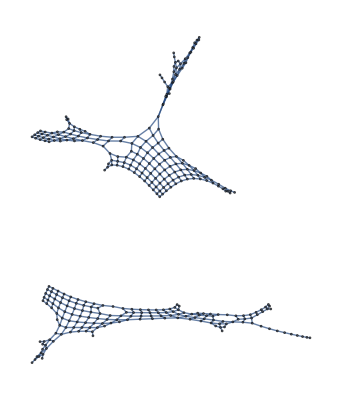

```mathematica
(*测试*)
initOldData=<|
"id_graph"->Graph[{}],
"manual_data_all"->goDict["data"],
"pieces_on_checkerboard"->{}
|>;
g=Fold[fGoGraph,initOldData,Values[goDict["data"]]];
g["id_graph"]
```

### 1.2.3 --可视化

```mathematica
(*初始状态*)
initOldData=<|
"id_graph"->Graph[{}],
"manual_data_all"->goDict["data"],
"pieces_on_checkerboard"->{}
|>;
(*每步，棋盘graph*)
checkerboardList={};
Do[
g=fGoGraph[If[k==1,initOldData,g],goDict["data"][[k]]];
AppendTo[checkerboardList,g["id_graph"]];
,{k,Length[goDict["data"]]}
];

(*可视化*)
Manipulate[
Graphics[{
GrayLevel[0.8],
(*棋盘*)
(*线*)
Line[{{1,#},{19,#}}]&/@Range[19],
Line[{{#,1},{#,19}}]&/@Range[19],
(*星位*)
PointSize[0.01],Point[goDict["position_to_xy"][#]]&/@{"PD","DD","DP","PP","JJ"},
(*同气棋子连线*)
Gray,
Thickness[0.015],
If[k>0,Line[{goDict["data"][#[[1]]]["position_xy"],goDict["data"][#[[2]]]["position_xy"]}]&/@EdgeList[checkerboardList[[k]]]],
(*棋子*)
If[k>0,
{
If[goDict["data"][#]["color"]=="B",GrayLevel[0.25],White],
EdgeForm[Directive[Thickness[0.002],Black]],
Disk[goDict["data"][#]["position_xy"],0.4]
}&/@VertexList[checkerboardList[[k]]]
]
},
PlotRange->{{0,20},{0,20}},
ImageSize->800],
{{k,0},0,Length[goDict["data"]],1}
]
```

### 1.2.4 f-输出JSON结果（用于后面绘图）

```mathematica
Association
```

```mathematica
fExportJSON[savePath_String,dbid_String,sgf_String]:=Module[{
goDict=fSGF2Dict[sgf],
initOldData,
checkerboardList={},
g,stepStatus
},
(*初始状态*)
initOldData=<|
"id_graph"->Graph[{}],
"manual_data_all"->goDict["data"],
"pieces_on_checkerboard"->{}
|>;
Do[
g=fGoGraph[If[k==1,initOldData,g],goDict["data"][[k]]];
AppendTo[checkerboardList,g["id_graph"]];
,{k,Length[goDict["data"]]}
];

stepStatus=Table[
If[k==1,
<|
"id"->k,
"add"->goDict["data"]/@VertexList[checkerboardList[[k]]],
"sub"->{}|>
,
<|
"id"->k,
"add"->goDict["data"]/@Complement[VertexList[checkerboardList[[k]]],VertexList[checkerboardList[[k-1]]]],
"sub"->goDict["data"]/@Complement[VertexList[checkerboardList[[k-1]]],VertexList[checkerboardList[[k]]]]|>
]
,{k,Length[checkerboardList]}];

Developer`WriteRawJSONFile[savePath,<|
"step_status"->stepStatus,
"db_id"->dbid,
"go_dict"->AssociateTo[goDict,{"data"->0}],
"sgf_string"->sgf
|>,"Compact"->1]
];
```

### 1.2.5 合并

```mathematica
fSGFExportJSON[dbid_,sgf_String]:=Module[{
goDict=fSGF2Dict[sgf],
savePath=FileNameJoin[{NotebookDirectory[],"export-data",StringTemplate["go-chess-manual-``.json"][dbid]}]
},
fExportJSON[savePath,dbid,sgf]
];
```

```mathematica
savePath=fSGFExportJSON[dbid,sgfString]
```

D:\github\gifor\usage-of-playing-go-chess\export-data\go-chess-manual-41341.json

```mathematica
temp=Developer`ReadRawJSONFile[savePath];
Keys[temp]
```

{step_status,db_id,sgf_string}

### 1.2.6 导出所有棋局

```mathematica
Dynamic[row]
savePaths=Table[fSGFExportJSON[row[[1]],row[[2]]],{row,strDatas}];
```

## 2. 棋盘、棋子、比赛信息

## 2.1 导入数据

```mathematica
SetDirectory[NotebookDirectory[]];
files=FileNames["*.json","export-data"];
jsonDatas=Developer`ReadRawJSONFile/@files;
Keys[jsonDatas[[1]]]
```

{step_status,db_id,go_dict,sgf_string}

```mathematica
sgfString=jsonDatas[[1]]["sgf_string"];
goDict=jsonDatas[[1]]["go_dict"];
stepStatus=jsonDatas[[1]]["step_status"];
bdid=jsonDatas[[1]]["bd_id"];
```

## 2.2 常量+标题

```mathematica
(*生成头部图像*)
fGenGIFInfo[goDict_]:=Module[{
goInfo,
imageHeader,
headerInfo,
headerWidth,headerHeight},
headerInfo=Column[{Style[goDict["info"]["比赛名称"],12,Bold,FontFamily->"微软雅黑"],
Style[goDict["info"]["比赛日期"],9,FontFamily->"微软雅黑"],

Row[Flatten@{
Style[goDict["info"]["执黑棋手"],10,Bold,FontFamily->"微软雅黑"],
Style[#,10,FontFamily->"微软雅黑"]&/@{"[执黑 ",goDict["info"]["黑棋段位"],"]"},
Style["   vs   ",10,FontFamily->"微软雅黑"],
Style[goDict["info"]["执白棋手"],10,Bold,FontFamily->"微软雅黑"],
Style[#,10,FontFamily->"微软雅黑"]&/@{"[执白 ",goDict["info"]["白棋段位"],"]"}
}],
Style[goDict["info"]["比赛结果"],10,FontFamily->"微软雅黑"],
Style["lixuan.xyz",10,FontFamily->"微软雅黑"]
},Alignment->Center];

imageHeader=Rasterize[headerInfo,ImageResolution->100];
imageHeader=ColorConvert[imageHeader,"RGB"];
{headerWidth,headerHeight}=ImageDimensions[imageHeader]+10;

goInfo=<|
"line_thickness"->1,(*线宽*)
"line_color"->0.8,(*线灰度*)
"space_thickness"->30,(*空宽，即两条线之间的空白宽度*)
"edge_thickness"->30,(*棋盘边界*)

"go_info_header"->imageHeader,(*[图片]标题*)
"go_info_header_width"->headerWidth,(*标题宽度*)
"go_info_header_height"->headerHeight(*标题宽度*)
|>;
AssociateTo[goInfo,
{
"gif_width"->19goInfo["line_thickness"]+18goInfo["space_thickness"]+2goInfo["edge_thickness"],(*棋盘宽度*)
"gif_height"->19goInfo["line_thickness"]+18goInfo["space_thickness"]+2goInfo["edge_thickness"]+headerHeight(*棋盘高度*)
}]
];

gifInfo=fGenGIFInfo[goDict]
```

<|line_thickness→1,line_color→0.8,space_thickness→30,edge_thickness→30,go_info_header→-Graphics-,go_info_header_width→323,go_info_header_height→128,gif_width→619,gif_height→747|>

## 2.3 棋子

```mathematica
(*生成普通棋子*)
genGIFPiece[gifInfo_]:=Module[{
pieceSize=Round[0.85(gifInfo["space_thickness"]+gifInfo["line_thickness"])]
},
<|
(*普通棋子*)
"img_black_piece"->ColorConvert[Rasterize[Graphics[{GrayLevel[0.3],EdgeForm[Directive[AbsoluteThickness[2],Black]],Disk[]}],ImageSize->pieceSize],"RGB"],
"img_white_piece"->ColorConvert[Rasterize[Graphics[{GrayLevel[0.9],EdgeForm[Directive[AbsoluteThickness[2],Black]],Disk[]}],ImageSize->pieceSize],"RGB"],

(*当前步棋子*)
"img_black_piece_current"->ColorConvert[Rasterize[Graphics[{GrayLevel[0.3],EdgeForm[Directive[AbsoluteThickness[2],Black]],Disk[],EdgeForm[],Red,Disk[{0,0},0.5]}],ImageSize->pieceSize],"RGB"],
"img_white_piece_current"->ColorConvert[Rasterize[Graphics[{GrayLevel[0.9],EdgeForm[Directive[AbsoluteThickness[2],Black]],Disk[],EdgeForm[],Red,Disk[{0,0},0.5]}],ImageSize->pieceSize],"RGB"]
|>
];

pieceNormal=genGIFPiece[gifInfo]
```

<|img_black_piece→-Graphics-,img_white_piece→-Graphics-,img_black_piece_current→-Graphics-,img_white_piece_current→-Graphics-|>

```mathematica
(*生成特殊棋子：棋盘上的线 —— 特殊的棋子 —— 用于提子时覆盖原棋子*)
genGIFChessboard[gifInfo_]:=Module[{
imgRC={gifInfo["space_thickness"]+gifInfo["line_thickness"],gifInfo["space_thickness"]+gifInfo["line_thickness"]},
st=gifInfo["space_thickness"],
lt=gifInfo["line_thickness"],
lineColor=gifInfo["line_color"],
semiLineTop,
semiLineBottom,
semiLineLeft,
semiLineRight,
centerPoint,
centerStar,
cross4
},
centerStar=SparseArray[{{i_,j_}/;(Abs[i-st/2-lt]+Abs[j-st/2-lt]<6)->0},imgRC,1];
centerPoint=SparseArray[{{i_,j_}/;(Abs[i-st/2-lt]<lt&&Abs[j-st/2-lt]<lt)->0},imgRC,1];
semiLineLeft=SparseArray[{{i_,j_}/;(st/2<i≤st/2+lt&&j<st/2+lt)->0},imgRC,1];
semiLineTop=Transpose[semiLineLeft];
semiLineRight=SparseArray[{{i_,j_}/;(st/2<i≤st/2+lt&&st/2+lt<j)->0},imgRC,1];
semiLineBottom=Transpose[semiLineRight];

<|
"img_cross_4"->ColorConvert[Image[Normal[centerPoint semiLineLeft semiLineTop semiLineRight semiLineBottom]/.(0->lineColor)],"RGB"],
"img_cross_star"->ColorConvert[Image[Normal[centerStar semiLineLeft semiLineTop semiLineRight semiLineBottom]/.(0->lineColor)],"RGB"],
"img_cross_3"->{
ColorConvert[Image[Normal[centerPoint semiLineLeft semiLineTop semiLineBottom]/.(0->lineColor)],"RGB"],
ColorConvert[Image[Normal[centerPoint semiLineLeft semiLineRight semiLineBottom]/.(0->lineColor)],"RGB"],
ColorConvert[Image[Normal[centerPoint semiLineTop semiLineRight semiLineBottom]/.(0->lineColor)],"RGB"],
ColorConvert[Image[Normal[centerPoint semiLineLeft semiLineTop semiLineRight]/.(0->lineColor)],"RGB"]
},
"img_cross_2"->{
ColorConvert[Image[Normal[centerPoint semiLineTop semiLineRight]/.(0->lineColor)],"RGB"],
ColorConvert[Image[Normal[centerPoint semiLineLeft semiLineTop]/.(0->lineColor)],"RGB"],
ColorConvert[Image[Normal[centerPoint semiLineLeft semiLineBottom]/.(0->lineColor)],"RGB"],
ColorConvert[Image[Normal[centerPoint semiLineRight semiLineBottom]/.(0->lineColor)],"RGB"]
}
|>
];
pieceSpecial=genGIFChessboard[gifInfo]
```

<|img_cross_4→-Graphics-,img_cross_star→-Graphics-,img_cross_3→{-Graphics-,-Graphics-,-Graphics-,-Graphics-},img_cross_2→{-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

## 2.4 坐标转换 + 棋盘

```mathematica
(*坐标转换：棋盘上的行列，转成Mma中ImageCompose的xy*)
(*输入
{行_从上数1~19，列_从左数1~19},gifInfo
*)
fPieceRC2XY[{r_,c_},gifInfo_]:=Module[{
stepLength=gifInfo["line_thickness"]+gifInfo["space_thickness"],
rc
},
(*转化为图像中的行数列数*)
rc={gifInfo["go_info_header_height"]+(r-1)stepLength,(c-1)stepLength}+gifInfo["edge_thickness"];
(**)
{rc[[2]],gifInfo["gif_height"]-rc[[1]]-1}
];

(*坐标转换：棋盘上的行列，转成GIF中的{left,top}*)
(*输入
{行_从上数1~19，列_从左数1~19},gifInfo
*)
fPieceRC2gifLT[{r_,c_},gifInfo_]:=Module[{
stepLength=gifInfo["line_thickness"]+gifInfo["space_thickness"]
},
(*转化为图像中的行数列数*)
{(c-1)stepLength,gifInfo["go_info_header_height"]+(r-1)stepLength}+gifInfo["edge_thickness"]-1
];


(* ========================================= *)
(*生成背景图像*)
fGenImageBasic[gifInfo_]:=Module[{
rangeStep=gifInfo["line_thickness"]+gifInfo["space_thickness"],
rangeAll=18(gifInfo["line_thickness"]+gifInfo["space_thickness"])+gifInfo["line_thickness"],
points=Flatten@Table[Range[gifInfo["line_thickness"]]+k (gifInfo["line_thickness"]+gifInfo["space_thickness"]),{k,0,18}],
rows,cols,matrix,
chessBoard
},
rows=Flatten@Outer[{#1,#2}->0.8&,points,Range[rangeAll]];
cols=Flatten@Outer[{#1,#2}->0.8&,Range[rangeAll],points];
matrix=SparseArray[rows~Join~cols,{rangeAll,rangeAll},1];

Image@ArrayPad[matrix,{{gifInfo["go_info_header_height"]+gifInfo["edge_thickness"],gifInfo["edge_thickness"]},{gifInfo["edge_thickness"],gifInfo["edge_thickness"]}},1];

chessBoard=ImageCompose[
(*棋盘方格*)
Image@ArrayPad[matrix,{{gifInfo["go_info_header_height"]+gifInfo["edge_thickness"],gifInfo["edge_thickness"]},{gifInfo["edge_thickness"],gifInfo["edge_thickness"]}},1], 
(*标题*)
gifInfo["go_info_header"],
{Center,Top},{Center,Top}];

Fold[ImageCompose[#1, pieceSpecial["img_cross_star"],fPieceRC2XY[#2,gifInfo],{Center,Center}]&,chessBoard,{{10,10},{4,4},{16,4},{4,16},{16,16}}]

];


imageBasic=fGenImageBasic[gifInfo];

imageBasicStar=Fold[ImageCompose[#1, pieceSpecial["img_cross_star"],fPieceRC2XY[#2,gifInfo],{Center,Center}]&,imageBasic,{{10,10},{4,4},{16,4},{4,16},{16,16}}];

imageBasicDemo=ImageCompose[imageBasicStar, pieceNormal["img_black_piece_current"],fPieceRC2XY[{3,3},gifInfo],{Center,Center}];
imageBasicDemo=ImageCompose[imageBasicDemo, pieceNormal["img_white_piece_current"],fPieceRC2XY[{5,5},gifInfo],{Center,Center}];
imageBasicDemo=ImageCompose[imageBasicDemo, pieceNormal["img_black_piece"],fPieceRC2XY[{7,7},gifInfo],{Center,Center}];
imageBasicDemo=ImageCompose[imageBasicDemo, pieceNormal["img_white_piece"],fPieceRC2XY[{9,9},gifInfo],{Center,Center}]
```

-Graphics-

## 2.6 全局颜色表

```mathematica
(*全局颜色表 - 棋子、棋盘、标题*)
fGlobalColorTable[imageDemo_,codeSize_]:=Module[{
image=ColorQuantize[imageDemo,2^codeSize,Method->"MedianCut"],
gct
},
gct=Union[Flatten[ImageData[image,"Byte"],1]];

<|
"global_color_table"->gct,
"global_color_table_index"-><|MapIndexed[#1->#2[[1]]-1&,gct]|>
|>
];

globalColorTable=fGlobalColorTable[imageBasicDemo,6];

(*图像转索引 ← 根据全局颜色表*)
fImage2Index[image_,colorTable_]:=Module[{imageData=Flatten[ImageData[image,"Byte"],1]},
Lookup[colorTable["global_color_table_index"],Key[#],Lookup[colorTable["global_color_table_index"],Key[Nearest[colorTable["global_color_table"],#,1][[1]]],0]]&/@imageData
];
```

## 2.7 素材的 LZW 数据

```mathematica
pieceNormal
pieceSpecial
```

<|img_black_piece→-Graphics-,img_white_piece→-Graphics-,img_black_piece_current→-Graphics-,img_white_piece_current→-Graphics-|>

<|img_cross_4→-Graphics-,img_cross_star→-Graphics-,img_cross_3→{-Graphics-,-Graphics-,-Graphics-,-Graphics-},img_cross_2→{-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

```mathematica
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"gif","variable_length_code_LZW_compression.wl"}]];

(*素材的 LZW 数据*)
lzwData=<|
"base_image"->VLZWCompress`VLZW[fImage2Index[imageBasic,globalColorTable],codeSize],
"piece"-><|
"black"->VLZWCompress`VLZW[fImage2Index[pieceNormal["img_black_piece"],globalColorTable],codeSize],
"white"->VLZWCompress`VLZW[fImage2Index[pieceNormal["img_white_piece"],globalColorTable],codeSize],
"black_current"->VLZWCompress`VLZW[fImage2Index[pieceNormal["img_black_piece_current"],globalColorTable],codeSize],
"white_current"->VLZWCompress`VLZW[fImage2Index[pieceNormal["img_white_piece_current"],globalColorTable],codeSize],

"size"->(<|"width"->#1,"height"->#2|>&@@ImageDimensions[pieceNormal["img_black_piece"]])
|>,
"line"-><|
"inner_normal"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_4"],globalColorTable],codeSize],
"inner_star"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_star"],globalColorTable],codeSize],

"edge_left"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_3"][[3]],globalColorTable],codeSize],
"edge_top"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_3"][[2]],globalColorTable],codeSize],
"edge_right"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_3"][[1]],globalColorTable],codeSize],
"edge_bottom"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_3"][[4]],globalColorTable],codeSize],

"corner_rt"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_2"][[3]],globalColorTable],codeSize],
"corner_lt"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_2"][[4]],globalColorTable],codeSize],
"corner_lb"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_2"][[1]],globalColorTable],codeSize],
"corner_rb"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_2"][[2]],globalColorTable],codeSize],

"size"->(<|"width"->#1,"height"->#2|>&@@ImageDimensions[pieceSpecial["img_cross_4"]])
|>
|>;
```

## 3. 导出GIF图像

## 3.1 导入GIF程序包

```mathematica
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"gif","gif_encode__global_color_table.wl"}]]
```

```mathematica
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"gif","variable_length_code_LZW_compression.wl"}]];
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"gif","gif_encode__global_color_table.wl"}]];
```

```mathematica
?VLZWCompress`VLZW
?GIFEncodeGCT`gif
```

## 3.2 棋谱数据 → LZW

```mathematica
(*落子*)
fAddPiece[add_,current_,lzwData_:lzwData,gifInfo_:gifInfo,delayTime_:50]:=Table[<|
"id"->a["id"],
"position"->(<|"left"->#1-Floor[lzwData["piece"]["size"]["width"]/2]+1,"top"->#2-Floor[lzwData["piece"]["size"]["height"]/2]+1|>&@@fPieceRC2gifLT[a["position_matirx"],gifInfo]),
"delay_time"->delayTime,
"frame_size"->lzwData["piece"]["size"],
"data_lzw"->If[a["color"]=="B",
If[current,lzwData["piece"]["black_current"],lzwData["piece"]["black"]],
If[current,lzwData["piece"]["white_current"],lzwData["piece"]["white"]]
]
|>,{a,add}];

(*提子*)
fSubPiece[sub_,lzwData_:lzwData,gifInfo_:gifInfo]:=Table[<|
"id"->s["id"],
"position"-><|"left"->#1-Floor[lzwData["line"]["size"]["width"]/2]+1,"top"->#2-Floor[lzwData["line"]["size"]["height"]/2]+1|>&@@fPieceRC2gifLT[s["position_matirx"],gifInfo],
"delay_time"->0,
"frame_size"->lzwData["line"]["size"],
"data_lzw"->Piecewise[{
{lzwData["line"]["corner_rt"],s["position_matirx"]=={1,19}},
{lzwData["line"]["corner_lt"],s["position_matirx"]=={1,1}},
{lzwData["line"]["corner_lb"],s["position_matirx"]=={19,1}},
{lzwData["line"]["corner_rb"],s["position_matirx"]=={19,19}},

{lzwData["line"]["edge_left"],s["position_matirx"][[2]]==1},
{lzwData["line"]["edge_top"],s["position_matirx"][[1]]==1},
{lzwData["line"]["edge_right"],s["position_matirx"][[2]]==19},
{lzwData["line"]["edge_bottom"],s["position_matirx"][[1]]==19},

{lzwData["line"]["inner_star"],MemberQ[{"JJ","DD","PD","DP","PP"},s["position_letter"]]}
},
lzwData["line"]["inner_normal"]]
|>,{s,sub}];


(*生成GIF数据流*)
gifImageData=Flatten[{<|"position"-><|"left"->0,"top"->0|>,"delay_time"->10,"frame_size"-><|"width"->gifInfo["gif_width"],"height"->gifInfo["gif_height"]|>,"data_lzw"->lzwData["base_image"]|>}~Join~Table[
{fAddPiece[step["add"],True,lzwData,gifInfo,50],fSubPiece[step["sub"],lzwData,gifInfo],fAddPiece[step["add"],False,lzwData,gifInfo,50]}
,{step,stepStatus}]];

imageSize=<|"width"->gifInfo["gif_width"],"height"->gifInfo["gif_height"]|>;
GIFEncodeGCT`gif["D:/t.gif",imageSize,globalColorTable["global_color_table"],gifImageData,Infinity];
```

## 4. 整合

```mathematica
(*需要其它3个包*)
fExportGif[savePath_,goDict_,codeSize_,delayTime_:50]:=Module[{
gifInfo=fGenGIFInfo[goDict],
pieceNormal,pieceSpecial,
imageBasic,imageBasicStar,imageBasicDemo,
globalColorTable,lzwData,
gifImageData
},
pieceNormal=genGIFPiece[gifInfo];
pieceSpecial=genGIFChessboard[gifInfo];

imageBasic=fGenImageBasic[gifInfo];
imageBasicStar=Fold[ImageCompose[#1, pieceSpecial["img_cross_star"],fPieceRC2XY[#2,gifInfo],{Center,Center}]&,imageBasic,{{10,10},{4,4},{16,4},{4,16},{16,16}}];
imageBasicDemo=ImageCompose[imageBasicStar, pieceNormal["img_black_piece_current"],fPieceRC2XY[{3,3},gifInfo],{Center,Center}];
imageBasicDemo=ImageCompose[imageBasicDemo, pieceNormal["img_white_piece_current"],fPieceRC2XY[{5,5},gifInfo],{Center,Center}];
imageBasicDemo=ImageCompose[imageBasicDemo, pieceNormal["img_black_piece"],fPieceRC2XY[{7,7},gifInfo],{Center,Center}];
imageBasicDemo=ImageCompose[imageBasicDemo, pieceNormal["img_white_piece"],fPieceRC2XY[{9,9},gifInfo],{Center,Center}];

globalColorTable=fGlobalColorTable[imageBasicDemo,codeSize];

lzwData=<|
"base_image"->VLZWCompress`VLZW[fImage2Index[imageBasic,globalColorTable],codeSize],
"piece"-><|
"black"->VLZWCompress`VLZW[fImage2Index[pieceNormal["img_black_piece"],globalColorTable],codeSize],
"white"->VLZWCompress`VLZW[fImage2Index[pieceNormal["img_white_piece"],globalColorTable],codeSize],
"black_current"->VLZWCompress`VLZW[fImage2Index[pieceNormal["img_black_piece_current"],globalColorTable],codeSize],
"white_current"->VLZWCompress`VLZW[fImage2Index[pieceNormal["img_white_piece_current"],globalColorTable],codeSize],

"size"->(<|"width"->#1,"height"->#2|>&@@ImageDimensions[pieceNormal["img_black_piece"]])
|>,
"line"-><|
"inner_normal"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_4"],globalColorTable],codeSize],
"inner_star"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_star"],globalColorTable],codeSize],

"edge_left"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_3"][[3]],globalColorTable],codeSize],
"edge_top"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_3"][[2]],globalColorTable],codeSize],
"edge_right"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_3"][[1]],globalColorTable],codeSize],
"edge_bottom"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_3"][[4]],globalColorTable],codeSize],

"corner_rt"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_2"][[3]],globalColorTable],codeSize],
"corner_lt"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_2"][[4]],globalColorTable],codeSize],
"corner_lb"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_2"][[1]],globalColorTable],codeSize],
"corner_rb"->VLZWCompress`VLZW[fImage2Index[pieceSpecial["img_cross_2"][[2]],globalColorTable],codeSize],

"size"->(<|"width"->#1,"height"->#2|>&@@ImageDimensions[pieceSpecial["img_cross_4"]])
|>
|>;

(*生成GIF数据流*)
gifImageData=Flatten[{<|"position"-><|"left"->0,"top"->0|>,"delay_time"->delayTime,"frame_size"-><|"width"->gifInfo["gif_width"],"height"->gifInfo["gif_height"]|>,"data_lzw"->lzwData["base_image"]|>}~Join~Table[
{fAddPiece[step["add"],True,lzwData,gifInfo,delayTime],fSubPiece[step["sub"],lzwData,gifInfo],fAddPiece[step["add"],False,lzwData,gifInfo,delayTime]}
,{step,stepStatus}]];

GIFEncodeGCT`gif[savePath,<|"width"->gifInfo["gif_width"],"height"->gifInfo["gif_height"]|>,globalColorTable["global_color_table"],gifImageData,Infinity];
];
```

```mathematica
fExportGif["d:/t.gif",goDict,6,50]
```

```mathematica
16 28
```

448

```mathematica
32 14
28 16
29 16
```

448

448

```mathematica
28*2/6.0
```

9.33333